#### Problem description

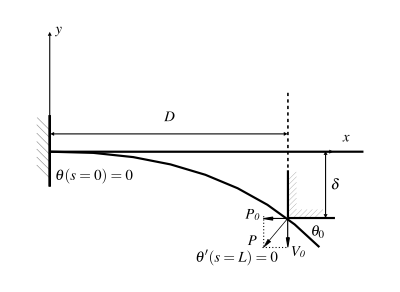

The governing equation for the Euler Elastica problem is

E I (d^2 θ)/(d s^2)-P_0 sin(θ)+ V_0 cos(θ)=0

where 0≤s≤L is the arc length coordinate, θ is the angle of deflection (in radians) at point s, P_0 (positive when pointing to right) and V_0(positive when pointing upward) are the horizontal and vertical forces at the right end of the beam, respectively.

Let ξ=s/L, then the equation becomes

(E I)/L^2 (d^2 θ)/dξ^2-P_0 sin(θ)+ V_0 cos(θ)=0

Note that

P_0=P sin(θ_0)<0
V_0=-P cos(θ_0)<0

where θ_0=θ(ξ=1), P>0 is the magnitude of the reaction force. Thus

(E I)/(P L^2) (d^2 θ)/(d ξ^2)-sin(θ_0)sin(θ)- cos(θ_0)cos(θ)=0
 (d^2 θ)/dξ^2-(P L^2)/(E I) cos(θ_0-θ)=0

Let k=(P L^2)/(E I), f=θ-θ_0. Note that

f(ξ=0)=θ(ξ=0)-θ_0=-θ_0
f(ξ=1)=θ(ξ=1)-θ_0=0
f'(ξ=1)=θ'(ξ=1)=0

The simplified governing equation and boundary conditions are as follows

(d^2 f)/dξ^2-k cos(f)=0
f(1)=0
f'(1)=0
f(0)=-θ_0

And we also have

D=L∫_0^1 cos(θ(ξ)) dξ=L∫_0^1 cos(f-f(0)) dξ
δ=L∫_0^1 sin(θ(ξ)) dξ=L∫_0^1 sin(f-f(0)) dξ
(P D^2)/(E I)=k (D/L)^2=(k(∫_0^1 cos(f-f(0)) dξ))^2
δ/D=(∫_0^1 sin(f-f(0)) dξ)/(∫_0^1 cos(f-f(0)) dξ)

### Moment-deflection relations

k=(P L^2)/(E I)
P_0=-tan(θ_0)V_0
V_0=-P cos(θ_0)
F=-2 V_0=2P cos(θ_0)
(F D^2)/(E I)=(P L^2)/(E I)2cos(θ_0)
(F D^2)/(E I)=2k cos(θ_0)
M=δ P_0+D V_0
M=(F D)/2(δ/D tan(θ_0)-1)
(M D)/(E I)=(F D^2)/(2 E I)(δ/D tan(θ_0)-1)
(M D)/(E I)=k (δ/D sin(θ_0)-cos(θ_0))

```mathematica
δPCurve=ParallelTable[solf=NDSolve[{f''[ξ]-k Cos[f[ξ]]==0,f[1]==0,f'[1]==0},f,{ξ,0,1}];DL=NIntegrate[Cos[(f[ξ]-f[0])/.solf[[1]]],{ξ,0,1}];
δL=NIntegrate[Sin[(f[ξ]-f[0])/.solf[[1]]],{ξ,0,1}];
{2k*DL^2 Cos[f[0]/.solf[[1]]],δL/DL,k,f[0]/.solf[[1]],k(δL/DL Sin[f[0]/.solf[[1]]]-Cos[f[0]/.solf[[1]]])},{k,0.02,3.43,0.02}];
```

δPCurve = {(F D^2)/(E I),δ/D,(P L^2)/(E I)=k,-θ_0,(M D)/(E I)}

```mathematica
Isp=δPCurve[[Position[δPCurve[[;;,1]],Max[δPCurve[[;;,1]]]][[1]]]][[1]]
```

{1.66795,-0.477411,1.36,0.669755,-1.46927}

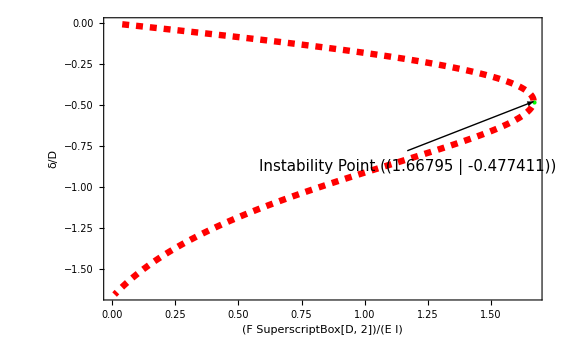

```mathematica
ListPlot[δPCurve[[;;,1;;2]],Joined->False];
pIsp=Graphics[{PointSize[Large],Green,Point[Isp[[1;;2]]]}];
pArrow=Graphics[Arrow[{Isp[[1;;2]]+{-0.5,-0.3},Isp[[1;;2]]}]];
ptext=Graphics[Text[Style["Instability Point "@{Isp[[1;;2]]},FontSize->15],Isp[[1;;2]]+{-0.5,-0.4}]];
p1=ListPlot[δPCurve[[;;,1;;2]],Joined->True,PlotStyle->Directive[Red,Thickness[0.008],Dashed],PlotRange->Automatic,ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["(F SuperscriptBox[D, 2])/(E I)",Black,FontFamily->"Times",16],Style["δ/D",Black,FontFamily->"Times",16]}];
Show[p1,pIsp,pArrow,ptext]
```

```mathematica
Isp
```

{1.66795,-0.477411,1.36,0.669755,1.06378}

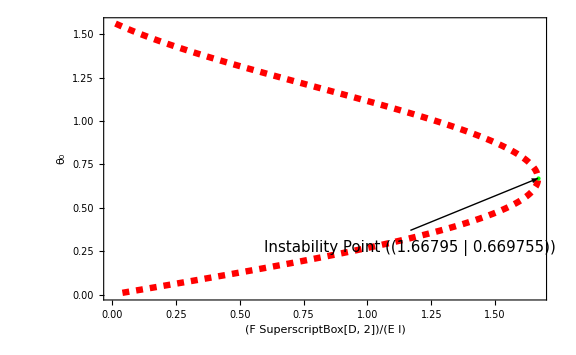

```mathematica
pIsp=Graphics[{PointSize[Large],Green,Point[Isp[[1;;4;;3]]]}];
pArrow=Graphics[Arrow[{Isp[[1;;4;;3]]+{-0.5,-0.3},Isp[[1;;4;;3]]}]];
ptext=Graphics[Text[Style["Instability Point "@{Isp[[1;;4;;3]]},FontSize->15],Isp[[1;;4;;3]]+{-0.5,-0.4}]];
p2=ListPlot[δPCurve[[;;,1;;4;;3]],Joined->True,PlotStyle->Directive[Red,Thickness[0.008],Dashed],PlotRange->Automatic,ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["(F SuperscriptBox[D, 2])/(E I)",Black,FontFamily->"Times",16],Style["θ_0",Black,FontFamily->"Times",16]},
RotateLabel->False];
Show[p2,pIsp,pArrow,ptext]
```

### Displacement-k

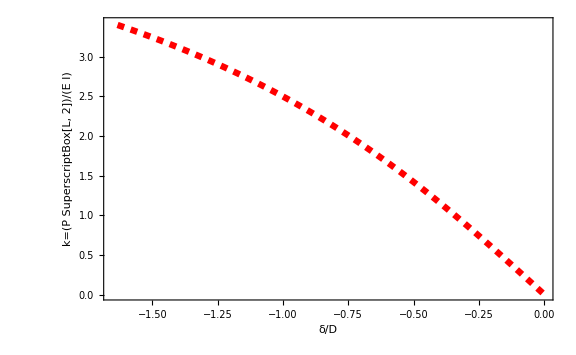

```mathematica
p3=ListPlot[δPCurve[[;;,2;;3;;1]],Joined->True,PlotStyle->Directive[Red,Thickness[0.008],Dashed],PlotRange->Automatic,ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["δ/D",Black,FontFamily->"Times",16],Style["k=(P SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",16]},RotateLabel->False]
```

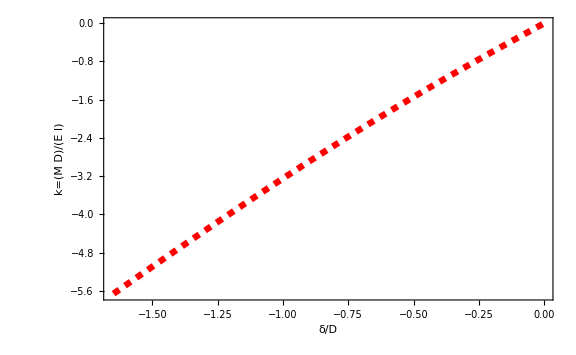

```mathematica
p4=ListPlot[δPCurve[[;;,{2,5}]],Joined->True,PlotStyle->Directive[Red,Thickness[0.008],Dashed],PlotRange->Automatic,ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["δ/D",Black,FontFamily->"Times",16],Style["(M D)/(E I)",Black,FontFamily->"Times",16]},RotateLabel->False]
```

### Several geometries

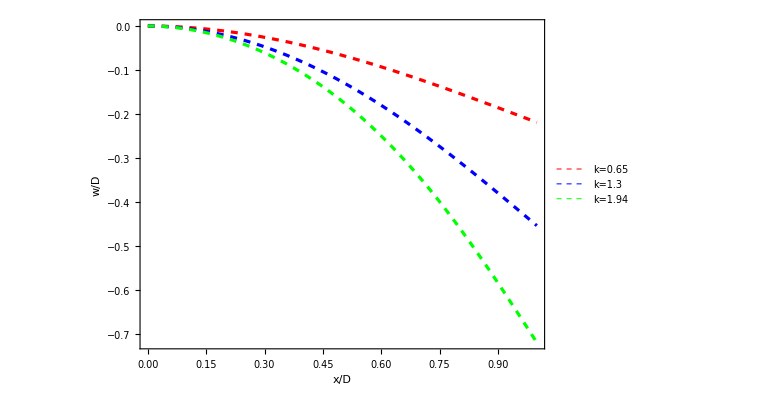

```mathematica
k=0.65;
solf=NDSolve[{f''[ξ]-k Cos[f[ξ]]==0,f[1]==0,f'[1]==0},f,{ξ,0,1}];
DL=NIntegrate[Cos[(f[ξ]-f[0])/.solf[[1]]],{ξ,0,1}];
solx = NDSolve[{x'[s]==Cos[f[s]-f[0]/.solf[[1]]],x[0]==0},x[s],{s,0,1}];
soly = NDSolve[{y'[s]==Sin[f[s]-f[0]/.solf[[1]]],y[0]==0},y[s],{s,0,1}];
pp1=ParametricPlot[{x[s]/DL/.solx[[1]],y[s]/DL/.soly[[1]]},{s,0,1},
PlotStyle->Directive[Red,Thickness[0.004],Dashed],
PlotLegends->Placed[{"k=0.65"},{0.36,0.7}]];
k=1.3;
solf=NDSolve[{f''[ξ]-k Cos[f[ξ]]==0,f[1]==0,f'[1]==0},f,{ξ,0,1}];
DL=NIntegrate[Cos[(f[ξ]-f[0])/.solf[[1]]],{ξ,0,1}];
solx = NDSolve[{x'[s]==Cos[f[s]-f[0]/.solf[[1]]],x[0]==0},x[s],{s,0,1}];
soly = NDSolve[{y'[s]==Sin[f[s]-f[0]/.solf[[1]]],y[0]==0},y[s],{s,0,1}];
pp2=ParametricPlot[{x[s]/DL/.solx[[1]],y[s]/DL/.soly[[1]]},{s,0,1},
PlotStyle->Directive[Blue,Thickness[0.004],Dashed],
PlotLegends->Placed[{"k=1.3"},{0.36,0.6}]];
k=1.94;
solf=NDSolve[{f''[ξ]-k Cos[f[ξ]]==0,f[1]==0,f'[1]==0},f,{ξ,0,1}];
DL=NIntegrate[Cos[(f[ξ]-f[0])/.solf[[1]]],{ξ,0,1}];
solx = NDSolve[{x'[s]==Cos[f[s]-f[0]/.solf[[1]]],x[0]==0},x[s],{s,0,1}];
soly = NDSolve[{y'[s]==Sin[f[s]-f[0]/.solf[[1]]],y[0]==0},y[s],{s,0,1}];
pp3=ParametricPlot[{x[s]/DL/.solx[[1]],y[s]/DL/.soly[[1]]},{s,0,1},
PlotStyle->Directive[Green,Thickness[0.004],Dashed],
PlotLegends->Placed[{"k=1.94"},{0.36,0.5}]];
Show[pp1,pp2,pp3,PlotRange->All,
ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["x/D",Black,FontFamily->"Times",16],Style["w/D",Black,FontFamily->"Times",16]}]
```

```mathematica
g[x_]:=0.00828565705323184+12066.251879963711 Sin[x]-18034.28488023207 Sin[2 x]+16469.808475543196 Sin[3 x]-10689.714347220814 Sin[4 x]+5035.9422971221375 Sin[5 x]-1666.9045009317156 Sin[6 x]+351.92785705840384 Sin[7 x]-36.145910349565575 Sin[8 x]
```

```mathematica
Pf=0.019127445571943
DD=0.001230994910676
EE=2.640322258060730*10^10
II=1.175968354361300*10^-19
(Pf DD^2)/(EE II)
```

0.0191274

0.00123099

2.64032×10^10

1.17597×10^-19

9.33506

Compare with experimental shape of EA

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
EA3z=Import["EA3z.m","List"]
```

{-5.45385×10^-6,4.08121×10^-6,0.0000117159,0.0000212509,0.0000288194,0.0000364541,0.0000440557,0.0000536238,0.0000631258,0.0000707605,0.0000802955,0.0000897975,0.0000974653,0.000107,0.000114602,0.000122237,0.000129904,0.000137506,0.000149008,0.000154676,0.00016231,0.000169945,0.00017758,0.000187148,0.000196749,0.000200484,0.000210052,0.000219653,0.000227288,0.00024069,0.000248324,0.000261759,0.000269361,0.000275095,0.000288497,0.000292265,0.000307667,0.000319135,0.000324869,0.000332537,0.000344039,0.000353673,0.000359407,0.000369009,0.000376742,0.000388277,0.000397845,0.00040938,0.000417081,0.000428615,0.000438184,0.000445917,0.000453618,0.000461286,0.000474787,0.000486355,0.000495989,0.000505624,0.000515291,0.000526826,0.00053456,0.000544194,0.000559695,0.000573262,0.000573196,0.000592597,0.000608065,0.000617765,0.000629366,0.000641,0.000648767,0.000660368,0.000673935,0.000687569,0.000691469,0.000699203,0.000710836,0.000714703,0.000724437,0.000732204,0.000739971,0.000747771,0.000757471,0.000763305,0.000771138,0.000778905,0.000784738,0.000796438,0.000806205,0.000813972,0.000823706,0.000835373,0.000850907,0.00086644,0.00087434,0.000886073,0.000897806,0.000905606,0.000917306,0.000927073,0.000929072,0.000948539,0.000958306,0.000981706,0.000991506,0.00103454,0.0010463,0.00105414,0.00106197,0.00107177,0.0010835,0.0010933,0.00110117,0.001109,0.00111687,0.0011247,0.00113254,0.00115023,0.00118937,0.001211,0.00122086}

```mathematica
Pf=0.019127445571943
DD=0.001230994910676
EE=2.640322258060730*10^10
II=1.175968354361300*10^-19
(Pf DD^2)/(EE II)
```

```mathematica
z=
```

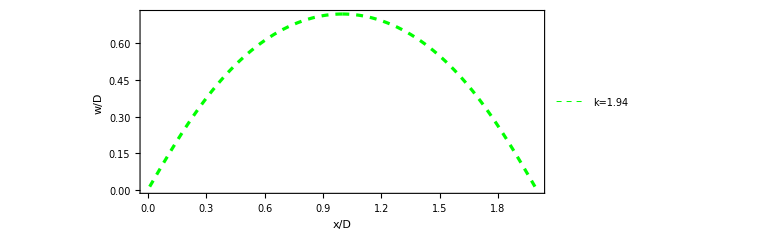

```mathematica
k=1.94;
solf=NDSolve[{f''[ξ]-k Cos[f[ξ]]==0,f[1]==0,f'[1]==0},f,{ξ,0,1}];
DL=NIntegrate[Cos[(f[ξ]-f[0])/.solf[[1]]],{ξ,0,1}];
solx = NDSolve[{x'[s]==-Cos[f[s]-f[0]/.solf[[1]]],x[1]==0},x[s],{s,0,1}];
soly = NDSolve[{y'[s]==Sin[f[s]-f[0]/.solf[[1]]],y[1]==0},y[s],{s,0,1}];
p3=ParametricPlot[{{x[s]/DL/.solx[[1]],y[s]/DL/.soly[[1]]},{2-x[s]/DL/.solx[[1]],y[s]/DL/.soly[[1]]}},{s,0,1},
PlotStyle->Directive[Green,Thickness[0.004],Dashed],
PlotLegends->Placed[{"k=1.94"},{0.5,0.5}],ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["x/D",Black,FontFamily->"Times",16],Style["w/D",Black,FontFamily->"Times",16]}]
```